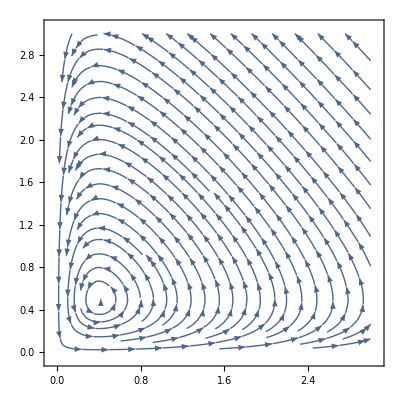

```mathematica
alpha = 0.5; gamma = 0.4;StreamPlot[{r*(alpha-s),s*(r-gamma)},{r,0,3},{s,0,3}]
```

```mathematica
system = {r'[t]==r[t]*(alpha-s[t]),s'[t]==s[t](r[t]-gamma)}
```

{r'[t]==r[t] (0.5-s[t]),s'[t]==(-0.4+r[t]) s[t]}

```mathematica
sol = DSolve[system,{r,s},t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{s→Function[{t},-0.5 ProductLog[-((2. 2.71828^(-1. C[1]+2. InverseFunction[∫_1^#1 1/(K[1] (1+ProductLog[-((29924061/325368125)^(C[1]-2 K[1]) 2^(1+2 C[1]-4 K[1]))/K[1]^(4/5)]))ⅆK[1]&][0.5 t+C[2]]))/(InverseFunction[∫_1^#1 1/(K[1] (1+ProductLog[-((29924061/325368125)^(C[1]-2 K[1]) 2^(1+2 C[1]-4 K[1]))/K[1]^(4/5)]))ⅆK[1]&][0.5 t+C[2]])^(4/5))]],r→Function[{t},InverseFunction[∫_1^#1 1/(K[1] (1+ProductLog[-((29924061/325368125)^(C[1]-2 K[1]) 2^(1+2 C[1]-4 K[1]))/K[1]^(4/5)]))ⅆK[1]&][0.5 t+C[2]]]}}